```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
a=0.4;
b=0.3;
c={0.5,0.5};
d=0.1;
```

```mathematica
θ=2π-π/4;
```

```mathematica
R[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}
```

```mathematica
(*check for mu*)
```

```mathematica
tt=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/curvature/discontinuous/solution/mu.csv"]
tt=Table[{tt[[i,2]],tt[[i,3]],tt[[i,1]]},{i,2,Length[tt]}]
```

```mathematica
y[s_]:=c+R[θ].{a Cos[2 π s]/(2+Cos[2 π s]),b Sin[2π s]}
u[y_]:={d y[[1]],-d y[[2]]}
(*this is the current position vector*)
x[s_]:=y[s]+u[y[s]]
e[s_]:=x'[s]
n[s_]:={-x'[s][[2]],x'[s][[1]]}/Norm[e[s]]
```

```mathematica
y[s]
```

{0.5+(0.282843 Cos[2 π s])/(2+Cos[2 π s])+0.212132 Sin[2 π s],0.5-(0.282843 Cos[2 π s])/(2+Cos[2 π s])+0.212132 Sin[2 π s]}

```mathematica
y'[s]
```

{1.33286 Cos[2 π s]+(1.77715 Cos[2 π s] Sin[2 π s])/(2+Cos[2 π s])^2-(1.77715 Sin[2 π s])/(2+Cos[2 π s]),1.33286 Cos[2 π s]-(1.77715 Cos[2 π s] Sin[2 π s])/(2+Cos[2 π s])^2+(1.77715 Sin[2 π s])/(2+Cos[2 π s])}

```mathematica
g[s_]:=e[s].e[s]
```

```mathematica
bb[s_]:=e'[s].n[s]
```

```mathematica
H[s_]:=1/(2g[s]) bb[s]
```

```mathematica
y[s]
```

{0.5+(0.282843 Cos[2 π s])/(2+Cos[2 π s])+0.212132 Sin[2 π s],0.5-(0.282843 Cos[2 π s])/(2+Cos[2 π s])+0.212132 Sin[2 π s]}

```mathematica
{0.5+(0.15307337294603593 Cos[2 π s])/(2+Cos[2 π s])+0.27716385975338603 Sin[2 π s],0.5-(0.36955181300451473 Cos[2 π s])/(2+Cos[2 π s])+0.11480502970952693 Sin[2 π s]}
```

{0.5+(0.153073 Cos[2 π s])/(2+Cos[2 π s])+0.277164 Sin[2 π s],0.5-(0.369552 Cos[2 π s])/(2+Cos[2 π s])+0.114805 Sin[2 π s]}

```mathematica
y'[s]
```

{1.33286 Cos[2 π s]+(1.77715 Cos[2 π s] Sin[2 π s])/(2+Cos[2 π s])^2-(1.77715 Sin[2 π s])/(2+Cos[2 π s]),1.33286 Cos[2 π s]-(1.77715 Cos[2 π s] Sin[2 π s])/(2+Cos[2 π s])^2+(1.77715 Sin[2 π s])/(2+Cos[2 π s])}

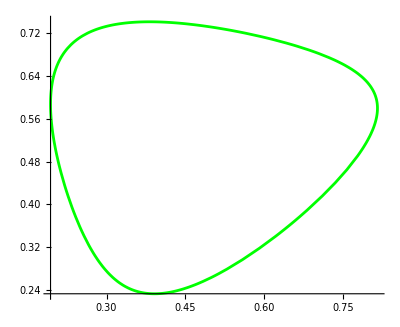

```mathematica
plotx=ParametricPlot[x[s],{s,0,1},PlotStyle->{Green}]
```

```mathematica
(*IMPORTANT: to compare with the numerical solution, here I plot g[s], H[s], ... on to of the REFERENCE curve y[s], not on top of the current one. In fact, in the numerical calculation g, H, .... take the correct values when computed on \partial \Omega^y_circle, not on \partial \Omega_circle*)
```

```mathematica
plotexact=ParametricPlot3D[{y[s][[1]],y[s][[2]],H[s]},{s,0,1},PlotStyle->{Blue}]
```

-Graphics3D-

```mathematica
plotnum=ListPointPlot3D[tt,PlotRange->Full,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[plotexact,plotnum,BoxRatios->{1,1,0.5}]
```

-Graphics3D-